```mathematica
files=FileNames["*.xlsx",NotebookDirectory[]]
```

{/Volumes/GoogleDrive/Мой диск/!МФТИ/Сollective intelligence 827/Лабы/2.1.6/2.1.6.xlsx,/Volumes/GoogleDrive/Мой диск/!МФТИ/Сollective intelligence 827/Лабы/2.1.6/wolfram2.1.6.xlsx,/Volumes/GoogleDrive/Мой диск/!МФТИ/Сollective intelligence 827/Лабы/2.1.6/~$2.1.6.xlsx,/Volumes/GoogleDrive/Мой диск/!МФТИ/Сollective intelligence 827/Лабы/2.1.6/~$wolfram2.1.6.xlsx}

```mathematica
importfile = files⟦2⟧
```

/Volumes/GoogleDrive/Мой диск/!МФТИ/Сollective intelligence 827/Лабы/2.1.6/wolfram2.1.6.xlsx

```mathematica
raw = Import[importfile];
```

```mathematica
makeAssoc[header_][row_]:=<|header->row//Thread|>;
makeDataset@raw_:=With[{header=raw⟦1⟧,data=raw⟦2;;⟧},
makeAssoc@header/@data
]//Dataset;
```

## Dataset1

```mathematica
dataset1=makeDataset[raw⟦1⟧]
```

Dataset[<>]

```mathematica
dataset1WithErrs=dataset1[All,<|"P"->(Around[#P,#dP]&),"Delta T"->(Around[#DT,#sT]&)|>]
```

Dataset[<>]

```mathematica
line1=LinearModelFit[Normal@dataset1[All,{"P","DT"}/*Values],{1,x},x]
line1["ParameterTable"]
```

FittedModel[0.513311+0.0100824 x]

| Estimate | Standard Error | t-Statistic | P-Value
1 | 0.513311 | 0.0794061 | 6.46438 | 0.00131918
x | 0.0100824 | 0.000302359 | 33.3459 | 4.55951×10^-7

## Dataset2

```mathematica
dataset2=makeDataset[raw⟦2⟧]
```

Dataset[<>]

```mathematica
dataset2WithErrs=dataset2[All,<|"P"->(Around[#P,#dP]&),"Delta T"->(Around[#DT,#sT]&)|>]
```

Dataset[<>]

```mathematica
line2=LinearModelFit[Normal@dataset2[All,{"P","DT"}/*Values],{1,x},x]
line2["ParameterTable"]
```

FittedModel[0.85224+0.00982854 x]

| Estimate | Standard Error | t-Statistic | P-Value
1 | 0.85224 | 0.0341078 | 24.9866 | 1.91576×10^-6
x | 0.00982854 | 0.00013092 | 75.0729 | 7.94444×10^-9

## Dataset3

```mathematica
dataset3=makeDataset[raw⟦3⟧]
```

Dataset[<>]

```mathematica
dataset3WithErrs=dataset3[All,<|"P"->(Around[#P,#dP]&),"Delta T"->(Around[#DT,#sT]&)|>]
```

Dataset[<>]

```mathematica
line3=LinearModelFit[Normal@dataset3[All,{"P","DT"}/*Values],{1,x},x]
line3["ParameterTable"]
```

FittedModel[0.661887+0.00978707 x]

| Estimate | Standard Error | t-Statistic | P-Value
1 | 0.661887 | 0.0677767 | 9.7657 | 0.00019151
x | 0.00978707 | 0.000258876 | 37.806 | 2.43922×10^-7

## Dataset4

```mathematica
dataset4=makeDataset[raw⟦4⟧]
```

Dataset[<>]

```mathematica
dataset4WithErrs=dataset4[All,<|"P"->(Around[#P,#dP]&),"Delta T"->(Around[#DT,#sT]&)|>]
```

Dataset[<>]

```mathematica
line4=LinearModelFit[Normal@dataset4[All,{"P","DT"}/*Values],{1,x},x]
line4["ParameterTable"]
```

FittedModel[1.0783+0.00819971 x]

| Estimate | Standard Error | t-Statistic | P-Value
1 | 1.0783 | 0.0254909 | 42.3013 | 1.39296×10^-7
x | 0.00819971 | 0.0000966027 | 84.8807 | 4.30143×10^-9

## Dataset5

```mathematica
dataset5=makeDataset[raw⟦5⟧]
```

Dataset[<>]

```mathematica
dataset5WithErrs=dataset5[All,<|"P"->(Around[#P,#dP]&),"Delta T"->(Around[#DT,#sT]&)|>]
```

Dataset[<>]

```mathematica
line5=LinearModelFit[Normal@dataset5[All,{"P","DT"}/*Values],{1,x},x]
line5["ParameterTable"]
```

FittedModel[0.8693+0.0083813 x]

| Estimate | Standard Error | t-Statistic | P-Value
1 | 0.8693 | 0.0323307 | 26.8878 | 1.3308×10^-6
x | 0.0083813 | 0.000121557 | 68.9494 | 1.21528×10^-8

## Dataset6

```mathematica
dataset6=makeDataset[raw⟦6⟧]
```

Dataset[<>]

```mathematica
dataset6WithErrs=dataset6[All,<|"P"->(Around[#P,#dP]&),"Delta T"->(Around[#DT,#sT]&)|>]
```

Dataset[<>]

```mathematica
line6=LinearModelFit[Normal@dataset6[All,{"P","DT"}/*Values],{1,x},x]
line6["ParameterTable"]
```

FittedModel[0.886851+0.00746428 x]

| Estimate | Standard Error | t-Statistic | P-Value
1 | 0.886851 | 0.0436207 | 20.331 | 5.32502×10^-6
x | 0.00746428 | 0.000164006 | 45.5123 | 9.66972×10^-8

## Dataset7

```mathematica
dataset7=makeDataset[raw⟦7⟧]
```

Dataset[<>]

```mathematica
dataset7WithErrs=dataset7[All,<|"P"->(Around[#P,#dP]&),"Delta T"->(Around[#DT,#sT]&)|>]
```

Dataset[<>]

```mathematica
line7=LinearModelFit[Normal@dataset7[All,{"P","DT"}/*Values],{1,x},x]
line7["ParameterTable"]
```

FittedModel[0.512182+0.0068791 x]

| Estimate | Standard Error | t-Statistic | P-Value
1 | 0.512182 | 0.0360241 | 14.2178 | 0.0000310026
x | 0.0068791 | 0.000135444 | 50.7893 | 5.59292×10^-8

## Dataset8

```mathematica
dataset8=makeDataset[raw⟦8⟧]
```

Dataset[<>]

```mathematica
dataset8WithErrs=dataset8[All,<|"P"->(Around[#P,#dP]&),"Delta T"->(Around[#DT,#sT]&)|>]
```

Dataset[<>]

```mathematica
line8=LinearModelFit[Normal@dataset8[All,{"P","DT"}/*Values],{1,x},x]
line8["ParameterTable"]
```

FittedModel[1.17024+0.006584 x]

| Estimate | Standard Error | t-Statistic | P-Value
1 | 1.17024 | 0.0374924 | 31.2126 | 6.33705×10^-7
x | 0.006584 | 0.000140965 | 46.7067 | 8.49719×10^-8

## Ура, график

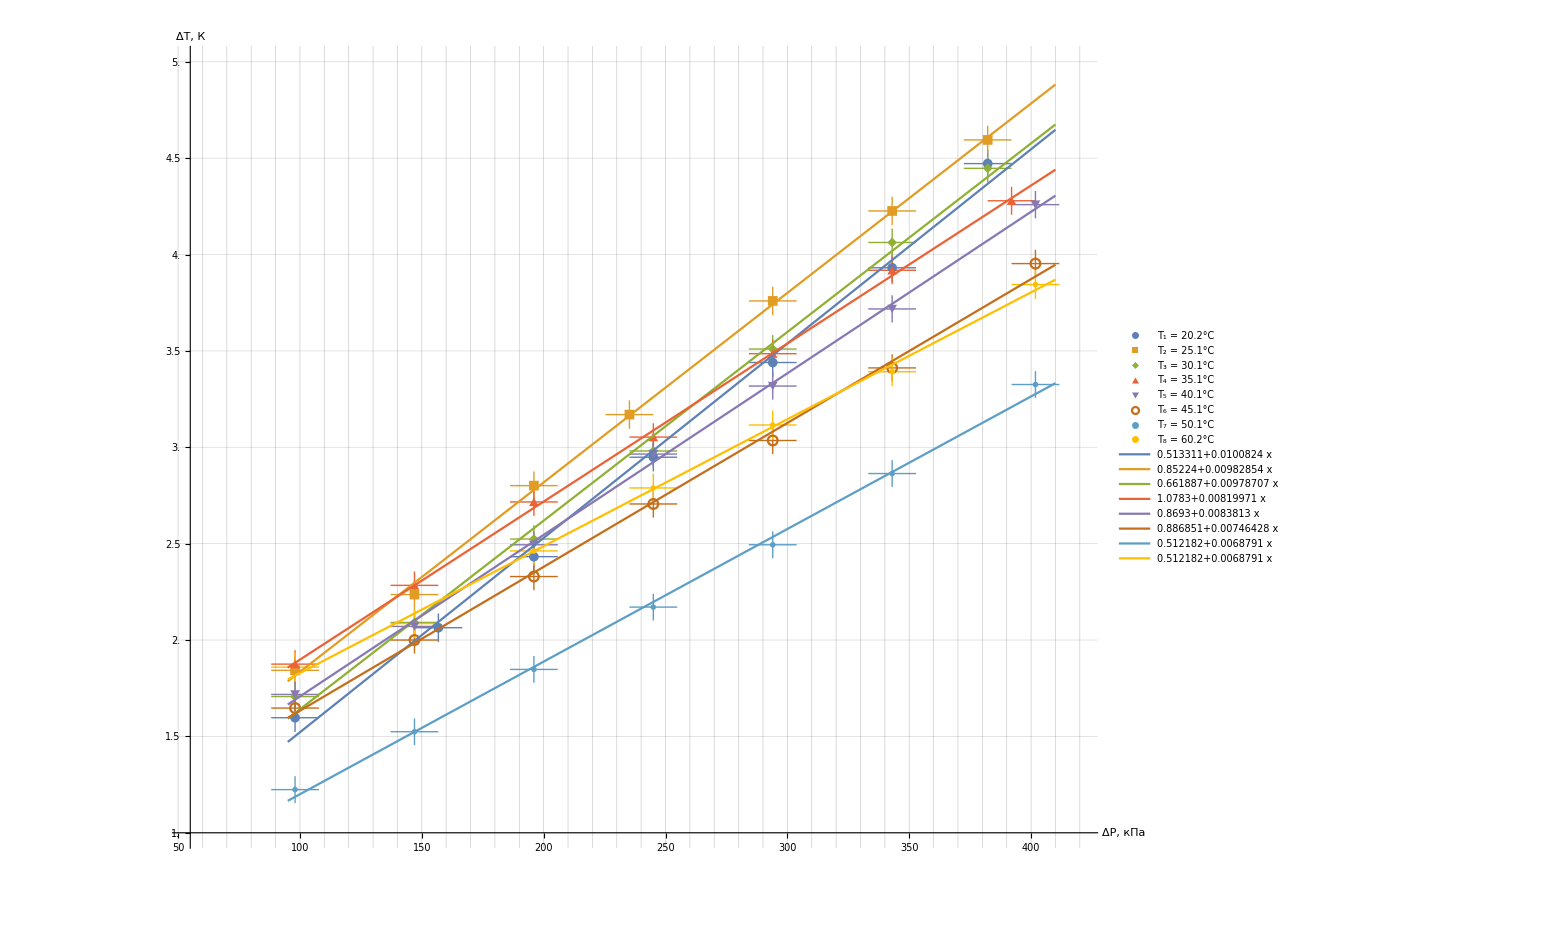

```mathematica
Show[
ListPlot[{dataset1WithErrs,dataset2WithErrs,dataset3WithErrs,dataset4WithErrs,dataset5WithErrs,dataset6WithErrs,dataset7WithErrs,dataset8WithErrs},
AxesLabel->{Style["ΔP, кПа",Large],Style["ΔT, К",Large]},
AxesStyle->Directive[Arrowheads[{0.02}],Black], 
ImageSize->1500,
GridLines->{Range[0,430,10], Range[0,10,0.25]},
Ticks-> {Range[0,420,50],Range[0,5,0.5]}, 
TicksStyle->20,
PlotRange->{{55,420},{1,5}},
PlotMarkers->{Automatic,Medium},
PlotLegends->Placed[LineLegend[
Automatic,
{"T_1 = 20.2°C","T_2 = 25.1°C","T_3 = 30.1°C","T_4 = 35.1°C","T_5 = 40.1°C","T_6 = 45.1°C","T_7 = 50.1°C","T_8 = 60.2°C"},
LegendMarkerSize->15,
LegendFunction->Framed,
LabelStyle->{FontSize->18}
],
{Scaled[0.85
],Scaled[0.2]}
]
],
Plot[
{line1@x,line2@x,line3@x,line4@x,line5@x,line6@x,line7@x,line8@x},{x,95,410},
PlotLegends->Placed[
LineLegend
[
Automatic,
Normal/@{line1,line2,line3,line4,line5,line6,line7,line7,line8},
LegendFunction->Framed,
LabelStyle->{FontSize->18}
],
{Scaled[0.2],Scaled[0.75]}
]
]
]
```

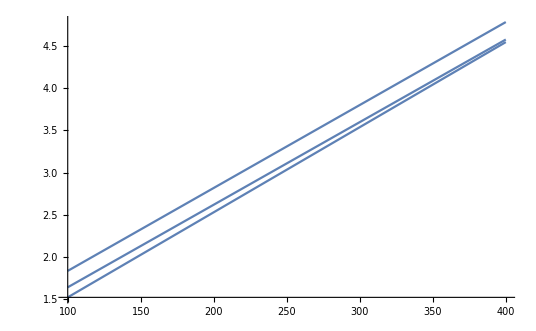

```mathematica
Show[
Plot[#[x]&/@{line1,line2,line3},{x,100,400},PlotStyle->Automatic]
]
```

```mathematica
Normal/@{line1,line2,line3,line4,line5,line6,line7,line7,line8}
```

{0.513311+0.0100824 x,0.85224+0.00982854 x,0.661887+0.00978707 x,1.0783+0.00819971 x,0.8693+0.0083813 x,0.886851+0.00746428 x,0.512182+0.0068791 x,0.512182+0.0068791 x,0.8693+0.0083813 x}